```mathematica
f=Import["C:\\Users\\Administrator\\Desktop\\RandomData\\12Data.txt"];
lst=StringSplit[f];
numLst={};
For[i=1,i≤Length[lst],i++,AppendTo[numLst,FromDigits[lst[[i]],16]]];
Length[numLst]
```

76666

```mathematica
1076/60
```

269/15

```mathematica
N[269/15]
```

17.9333

```mathematica
Max[numLst]
```

22126

```mathematica
Length[lst]
```

58005

```mathematica
numLst[1;;20]
```

{127,96,104,100,73,60,40,22,7,4,0,0,2,11,14,26,32,23,20,15,11,8,5,0,2,4,11,17,31,57,51,74,123,135,118,113,122,128,137,156,192,191,169,57919,49,87,139,153,131,95,83,89,74,67,71,66,45,40,64,98,134,130,96,83,86,57,54,58,66,45,45,78,107,131,131,107,80,78,82,73,71,67,43,47,87,136,158}[1]
 |  |  |  |

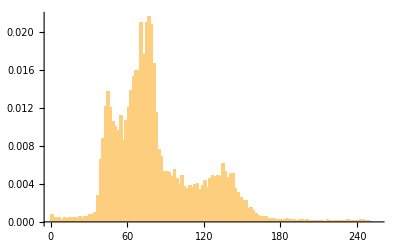

```mathematica
Histogram[numLst,{0,256,2},"PDF"]
```

```mathematica
Length[numLst]
```

944

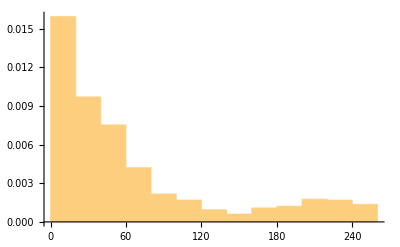

```mathematica
Histogram[numLst,Automatic,"PDF"]
```